```mathematica
Clear["Global`*"]
```

```mathematica
(* Definitions *)
oneJump[rx_,ry_,μx_,μy_,σ2_]:=(2π σ2)^-1 Exp[-((rx-μx)^2+(ry-μy)^2)/(2σ2)];
normalPDF[z_,μz_,σ2_]:=(2 π σ2)^(-1/2)Exp[-(z-μz)^2/(2σ2)]
InvChi2[σ2_,ν1_,σ12_]:=(ν1 σ12/2)^(ν1/2)/Gamma[ν1/2] σ2^(-ν1/2-1)Exp[-(ν1 σ12)/(2σ2)];
likelihood[rxMean_,ryMean_,V_,n_,μx_,μy_,σ2_]:=(2π σ2)^-n Exp[-(n(rxMean-μx)^2+n(ryMean-μy)^2+n V)/(2σ2)]
priorForce[μx_,μy_,σ2_,μxp_,μyp_,κp_,νp_,σp2_]:=normalPDF[μx,μxp,σ2/κp]*normalPDF[μy,μyp,σ2/κp]*InvChi2[σ2,νp,σp2]
npRules = {νp->2 np-2,κp->np,σp2->np Vp/(2np-2)};
```

```mathematica
(* Calculate null-model prior *)
priorNoForce = Integrate[priorForce[μx,μy,σ2,μxp,μyp,κp,νp,σp2],{μx,-∞,∞},{μy,-∞,∞},Assumptions->{σ2>0,κp>0}]
```

(2^(-νp/2) ⅇ^(-(νp σp2)/(2 σ2)) ((νp σp2)/σ2)^(νp/2))/(σ2 Gamma[νp/2])

```mathematica
(* Check norms *)
Integrate[oneJump[rx,ry,μx,μy,σ2],{rx,-∞,∞},{ry,-∞,∞},Assumptions->σ2>0]
Integrate[normalPDF[z,μ,σ2],{z,-∞,∞},Assumptions->σ2>0]
Integrate[likelihood[rxMean,ryMean,V,n,μx,μy,σ2],{rxMean,-∞,∞},{ryMean,-∞,∞},Assumptions->{σ2>0,n>0}];
Integrate[%,{V,0,∞},Assumptions->{σ2>0,n>0}]; (* This one does not have to integrate out, because it needs a Jacobian *)
```

1

1

(2^(2-n) π^(1-n) σ2^(2-n))/n^2

```mathematica
(* Calculate data likelihood for H1F *)
LH1a=Integrate[likelihood[rxMean,ryMean,V,n,μx,μy,σ2] * priorForce[μx,μy,σ2,μxp,μyp,κp,νp,σp2],{μx,-∞,∞},Assumptions->{σ2>0,n>0,κp>0}];
LH1b=Integrate[LH1a,{μy,-∞,∞},Assumptions->{σ2>0,n>0,κp>0}]
```

(2^(-n-νp/2) ⅇ^(-(n^2 V+κp νp σp2+n (rxMean^2 κp+ryMean^2 κp+V κp-2 rxMean κp μxp+κp μxp^2-2 ryMean κp μyp+κp μyp^2+νp σp2))/(2 (n+κp) σ2)) π^-n κp σ2^(-1-n) ((νp σp2)/σ2)^(νp/2))/((n+κp) Gamma[νp/2])

```mathematica
LH1c=Integrate[LH1b,{σ2,0,∞},Assumptions->{κp>0,n>0,νp>0,σp2>0,V>0,rxMean∈Reals,ryMean∈Reals,μxp ∈Reals,μyp ∈ Reals}]
```

1/Gamma[νp/2]π^-n κp (n+κp)^(-1+n+νp/2) (νp σp2)^(νp/2) (1/(n (n V+κp (V+(rxMean-μxp)^2+(ryMean-μyp)^2))+(n+κp) νp σp2))^(n+νp/2) Gamma[n+νp/2]

```mathematica
LH1=LH1c/.npRules//Simplify
```

1/(Vp Gamma[-1+np])(n+np)^(-2+n+np) π^-n (np Vp)^np (1/(n^2 V+np^2 Vp+n np (rxMean^2+ryMean^2+V+Vp-2 rxMean μxp+μxp^2-2 ryMean μyp+μyp^2)))^(-1+n+np) Gamma[-1+n+np]

```mathematica
(* Calculate data likelihood for H0F *)
LH0a=Integrate[
likelihood[rxMean,ryMean,V,n,λ gx dt,λ gy dt,σ2]*priorNoForce,{σ2,0,∞},Assumptions->{κp>0,n>0,νp>0,σp2>0,V>0,rxMean∈Reals,ryMean∈Reals,dt>0,λ>0,gx ∈Reals,gy ∈ Reals}]
```

1/Gamma[νp/2]π^-n (νp σp2)^(νp/2) (1/(n (rxMean^2+ryMean^2+V-2 dt (gx rxMean+gy ryMean) λ+dt^2 (gx^2+gy^2) λ^2)+νp σp2))^(n+νp/2) Gamma[n+νp/2]

```mathematica
LH0=LH0a/.npRules//Simplify
```

1/Gamma[-1+np]π^-n (np Vp)^(-1+np) (1/(np Vp+n (rxMean^2+ryMean^2+V-2 dt gx rxMean λ-2 dt gy ryMean λ+dt^2 gx^2 λ^2+dt^2 gy^2 λ^2)))^(-1+n+np) Gamma[-1+n+np]

```mathematica
(* Get the Bayes factor B10F *)
B10Fa=LH1/LH0//FullSimplify;
B10Fb=(B10Fa//.{((rxMean-μxp)^2+(ryMean-μyp)^2)->(rMean-μp)^2,(rxMean^2+ryMean^2)->rMean^2,gx->√(g^2-gy^2),gx rxMean->g rMean-gy ryMean})//FullSimplify
```

np (n+np)^(-2+n+np) (1/(np Vp+n (V+(rMean-dt g λ)^2)))^(1-n-np) (1/(n^2 V+np^2 Vp+n np (V+Vp+(rMean-μp)^2)))^(-1+n+np)

```mathematica
(* Combine powers for 1D and 2D expressions *)
p[d_]:=d (n+np)/2+k d + c;
eqs={p[1]==(n+np-3)/2,p[2]==n+np-1};
Solve[eqs,{k,c}]
```

{{k→1/2,c→-2}}

```mathematica
(* Calculates the limit of zeta_t_perp *)
zetaTPerp = √(v0(1-(B/η)^(1/p))/((B/η)^(1/p)η^2-1));
zetaTPerp/.{v0->1+u np/n, η->√(np/(n+np)),p->d((n+np+1)/2)-2}//.{n->1/x};
Series[%,{x,0,1}]
```

√2 √(Log[B/(√np √x)]/d) √x+O[x]^(3/2)

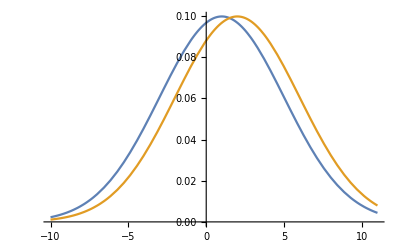

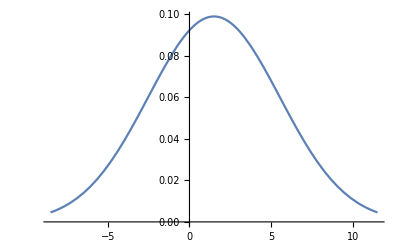

1/(√(2 π) (1/(√(2 π) σ^2)+(ⅇ^(-1/(2 σ^4)))/(√(2 π) σ^2)) σ^2)

0.507812

```mathematica
normPDF[x_,μ_,σ_]:=PDF[NormalDistribution[μ,σ^2]][x]
Plot[{normPDF[x,1,2],normPDF[x,2,2],(normPDF[x,1,2]+normPDF[x,2,2])/2},{x,-10,11}]
Plot[(normPDF[x,1,2]+normPDF[x,2,2])/2,{x,1.5-10,1.5+10}]
normPDF[1,1,σ]/(normPDF[1,1,σ]+normPDF[1,2,σ])
%/.σ->2.
```

```mathematica
.
```